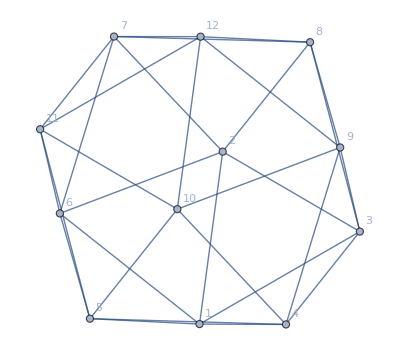

```mathematica
Graph[plantri[[1]],VertexLabels->"Name"]
```

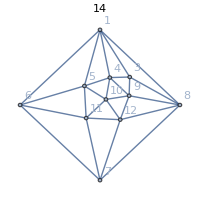
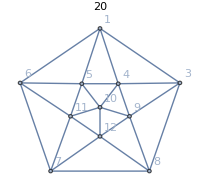
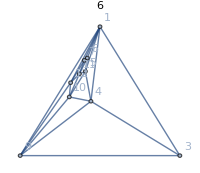
{{-Graphics-, | 1 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12
1 | 14
 | 
14 | 
14 | 
14 | 
14 | 6
8 | 
14 | 9
5 | 4
10 | 6
8 | 1
13
3 |  | 14
 | 
14 | 8
6 | 4
10 | 4
10 | 
14 | 
14 | 4
10 | 
14 | 8
6
4 |  |  | 14
 | 
14 | 5
9 | 1
13 | 9
5 | 
14 | 
14 | 7
7 | 3
11
5 |  |  |  | 14
 | 
14 | 4
10 | 1
13 | 3
11 | 
14 | 
14 | 8
6
6 |  |  |  |  | 14
 | 
14 | 6
8 | 1
13 | 6
8 | 
14 | 4
10
7 |  |  |  |  |  | 14
 | 
14 | 5
9 | 6
8 | 
14 | 
14
8 |  |  |  |  |  |  | 14
 | 
14 | 4
10 | 6
8 | 
14
9 |  |  |  |  |  |  |  | 14
 | 
14 | 7
7 | 
14
10 |  |  |  |  |  |  |  |  | 14
 | 
14 | 
14
11 |  |  |  |  |  |  |  |  |  | 14
 | 
14
12 |  |  |  |  |  |  |  |  |  |  | 14
}full,{{-Graphics-, | 1 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12
1 | 20
 | 
20 | 
20 | 
20 | 
20 | 6
14 | 6
14 | 9
11 | 7
13 | 9
11 | 1
19
3 |  | 20
 | 
20 | 9
11 | 6
14 | 6
14 | 
20 | 
20 | 7
13 | 1
19 | 9
11
4 |  |  | 20
 | 
20 | 9
11 | 1
19 | 9
11 | 
20 | 
20 | 8
12 | 8
12
5 |  |  |  | 20
 | 
20 | 9
11 | 1
19 | 8
12 | 
20 | 
20 | 8
12
6 |  |  |  |  | 20
 | 
20 | 6
14 | 1
19 | 7
13 | 
20 | 9
11
7 |  |  |  |  |  | 20
 | 
20 | 9
11 | 7
13 | 
20 | 
20
8 |  |  |  |  |  |  | 20
 | 
20 | 7
13 | 9
11 | 
20
9 |  |  |  |  |  |  |  | 20
 | 
20 | 8
12 | 
20
10 |  |  |  |  |  |  |  |  | 20
 | 
20 | 
20
11 |  |  |  |  |  |  |  |  |  | 20
 | 
20
12 |  |  |  |  |  |  |  |  |  |  | 20
}{EdgeDelete,1<->8},{-Graphics-, | 1 | 3 | 4 | 5 | 6 | 7 | 9 | 10 | 11 | 12
1 | 6
 | 
6 | 
6 | 
6 | 
6 | 
6 | 
6 | 3
3 | 3
3 | 
6
3 |  | 6
 | 
6 | 1
5 | 2
4 | 2
4 | 
6 | 3
3 | 1
5 | 1
5
4 |  |  | 6
 | 
6 | 4
2 | 
6 | 
6 | 
6 | 1
5 | 5
1
5 |  |  |  | 6
 | 
6 | 5
1 | 5
1 | 
6 | 
6 | 
6
6 |  |  |  |  | 6
 | 
6 | 
6 | 1
5 | 
6 | 5
1
7 |  |  |  |  |  | 6
 | 4
2 | 1
5 | 
6 | 
6
9 |  |  |  |  |  |  | 6
 | 
6 | 1
5 | 
6
10 |  |  |  |  |  |  |  | 6
 | 
6 | 
6
11 |  |  |  |  |  |  |  |  | 6
 | 
6
12 |  |  |  |  |  |  |  |  |  | 6
}{EdgeContract,1<->8}}}

```mathematica
With[
{g=EdgeAdd[VertexDelete[Graph[plantri[[1]],VertexLabels->"Name"],2],{1<->8}]},
ColorMatrixForEdgeOperationMatrix[g,{1<->8},{EdgeDelete,EdgeContract}, 
Graph[#,GraphLayout->"TutteEmbedding",VertexLabels->"Name",PlotLabel->ChromaticPolynomial[#,4]/24,ImageSize->200]&,
{1,3,8,7,6}]/. 0->""
]
```

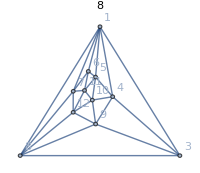
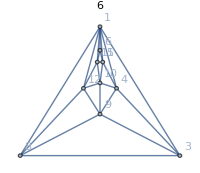
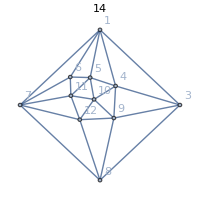
{{-Graphics-, | 1 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12
1 | 8
 | 
8 | 
8 | 
8 | 
8 | 
8 | 
8 | 6
2 | 1
7 | 6
2 | 1
7
3 |  | 8
 | 
8 | 4
4 | 2
6 | 4
4 | 
8 | 
8 | 3
5 | 
8 | 3
5
4 |  |  | 8
 | 
8 | 4
4 | 1
7 | 4
4 | 
8 | 
8 | 2
6 | 3
5
5 |  |  |  | 8
 | 
8 | 4
4 | 1
7 | 2
6 | 
8 | 
8 | 3
5
6 |  |  |  |  | 8
 | 
8 | 4
4 | 
8 | 3
5 | 
8 | 3
5
7 |  |  |  |  |  | 8
 | 
8 | 2
6 | 3
5 | 
8 | 
8
8 |  |  |  |  |  |  | 8
 | 
8 | 3
5 | 2
6 | 
8
9 |  |  |  |  |  |  |  | 8
 | 
8 | 6
2 | 
8
10 |  |  |  |  |  |  |  |  | 8
 | 
8 | 
8
11 |  |  |  |  |  |  |  |  |  | 8
 | 
8
12 |  |  |  |  |  |  |  |  |  |  | 8
}full,{{-Graphics-, | 1 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12
1 | 14
 | 
14 | 
14 | 
14 | 
14 | 6
8 | 
14 | 9
5 | 4
10 | 6
8 | 1
13
3 |  | 14
 | 
14 | 8
6 | 4
10 | 4
10 | 
14 | 
14 | 4
10 | 
14 | 8
6
4 |  |  | 14
 | 
14 | 5
9 | 1
13 | 9
5 | 
14 | 
14 | 7
7 | 3
11
5 |  |  |  | 14
 | 
14 | 4
10 | 1
13 | 3
11 | 
14 | 
14 | 8
6
6 |  |  |  |  | 14
 | 
14 | 6
8 | 1
13 | 6
8 | 
14 | 4
10
7 |  |  |  |  |  | 14
 | 
14 | 5
9 | 6
8 | 
14 | 
14
8 |  |  |  |  |  |  | 14
 | 
14 | 4
10 | 6
8 | 
14
9 |  |  |  |  |  |  |  | 14
 | 
14 | 7
7 | 
14
10 |  |  |  |  |  |  |  |  | 14
 | 
14 | 
14
11 |  |  |  |  |  |  |  |  |  | 14
 | 
14
12 |  |  |  |  |  |  |  |  |  |  | 14
}{EdgeDelete,1<->7},{-Graphics-, | 1 | 3 | 4 | 5 | 6 | 8 | 9 | 10 | 11 | 12
1 | 6
 | 
6 | 
6 | 
6 | 
6 | 
6 | 3
3 | 3
3 | 
6 | 
6
3 |  | 6
 | 
6 | 4
2 | 2
4 | 
6 | 
6 | 1
5 | 
6 | 5
1
4 |  |  | 6
 | 
6 | 1
5 | 5
1 | 
6 | 
6 | 5
1 | 
6
5 |  |  |  | 6
 | 
6 | 
6 | 1
5 | 
6 | 
6 | 5
1
6 |  |  |  |  | 6
 | 2
4 | 1
5 | 3
3 | 
6 | 1
5
8 |  |  |  |  |  | 6
 | 
6 | 1
5 | 4
2 | 
6
9 |  |  |  |  |  |  | 6
 | 
6 | 1
5 | 
6
10 |  |  |  |  |  |  |  | 6
 | 
6 | 
6
11 |  |  |  |  |  |  |  |  | 6
 | 
6
12 |  |  |  |  |  |  |  |  |  | 6
}{EdgeContract,1<->7}},{{-Graphics-, | 1 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12
1 | 14
 | 
14 | 
14 | 
14 | 
14 | 
14 | 6
8 | 6
8 | 4
10 | 9
5 | 1
13
3 |  | 14
 | 
14 | 5
9 | 4
10 | 6
8 | 
14 | 
14 | 6
8 | 1
13 | 4
10
4 |  |  | 14
 | 
14 | 8
6 | 1
13 | 4
10 | 
14 | 
14 | 3
11 | 8
6
5 |  |  |  | 14
 | 
14 | 9
5 | 1
13 | 7
7 | 
14 | 
14 | 3
11
6 |  |  |  |  | 14
 | 
14 | 4
10 | 
14 | 4
10 | 
14 | 8
6
7 |  |  |  |  |  | 14
 | 
14 | 6
8 | 4
10 | 
14 | 
14
8 |  |  |  |  |  |  | 14
 | 
14 | 6
8 | 5
9 | 
14
9 |  |  |  |  |  |  |  | 14
 | 
14 | 7
7 | 
14
10 |  |  |  |  |  |  |  |  | 14
 | 
14 | 
14
11 |  |  |  |  |  |  |  |  |  | 14
 | 
14
12 |  |  |  |  |  |  |  |  |  |  | 14
}{EdgeDelete,1<->8},{-Graphics-, | 1 | 3 | 4 | 5 | 6 | 7 | 9 | 10 | 11 | 12
1 | 6
 | 
6 | 
6 | 
6 | 
6 | 
6 | 
6 | 3
3 | 3
3 | 
6
3 |  | 6
 | 
6 | 1
5 | 2
4 | 2
4 | 
6 | 3
3 | 1
5 | 1
5
4 |  |  | 6
 | 
6 | 4
2 | 
6 | 
6 | 
6 | 1
5 | 5
1
5 |  |  |  | 6
 | 
6 | 5
1 | 5
1 | 
6 | 
6 | 
6
6 |  |  |  |  | 6
 | 
6 | 
6 | 1
5 | 
6 | 5
1
7 |  |  |  |  |  | 6
 | 4
2 | 1
5 | 
6 | 
6
9 |  |  |  |  |  |  | 6
 | 
6 | 1
5 | 
6
10 |  |  |  |  |  |  |  | 6
 | 
6 | 
6
11 |  |  |  |  |  |  |  |  | 6
 | 
6
12 |  |  |  |  |  |  |  |  |  | 6
}{EdgeContract,1<->8}}}

```mathematica
With[
{g=EdgeAdd[VertexDelete[Graph[plantri[[1]],VertexLabels->"Name"],2],{1<->7,1<->8}]},
ColorMatrixForEdgeOperationMatrix[g,{1<->7,1<->8},{EdgeDelete,EdgeContract}, 
Graph[#,GraphLayout->"TutteEmbedding",VertexLabels->"Name",PlotLabel->ChromaticPolynomial[#,4]/24,ImageSize->200]&,
{1,3,8,7,6}]/. 0->""
]
```